```mathematica
NN = 3000
Λ = 10
2.0 Log[Λ/m0]
Λ^2
cc[k_]  :=  Exp[ (ⅈ 2 π k)/NN]
circ= Array[cc, NN, 0];

3000
10
2. Log[10/m0]
100
sys[u_, m_] := {    1/NN ∑_(k=0)^(NN-1) Log [ DD + (σ - m circ[[k+1]])(σ - Conjugate[m circ[[k+1]]])] ==Log [ Λ^2],
            1/NN ∑_(k=0)^(NN-1) (σ - m circ[[k+1]]) Log [ 1 + DD/((σ - m circ[[k+1]])(σ - Conjugate[m circ[[k+1]]]))] == u σ };
sol[u_, m_]:=FindRoot[sys[u,m],{ σ , Λ Exp [ (- u)/2.0]2.0}, {DD,Λ^2 ( 1 - Exp[-u])2.0}]
sig[u_,m_]:= σ /. sol[u, m]
dd[u_, m_] := DD /. sol[u,m]
rsolve[u_] := NSolve[ x - Log[x] == 1. + u, x ]
r1[u_] :=  x /. rsolve[u][[1]]
r2[u_] :=  x /. rsolve[u][[2]]
```

3000

10

2. Log[10/m0]

100

3000

10

2. Log[10/m0]

100

```mathematica
sysappr[u_,m_] := { σ Log [ Λ^2/σ^2] - m^2/σ  == u σ }
solappr[u_,m_] := FindRoot[sysappr[u,m],{ σ , Λ Exp [ (- u)/2.0]2.0}];
asig[u_,m_] := σ /. solappr[u,m]
```

```mathematica
u= 0.005
m = 0.02
Λ Exp[-(u+1)/2]
```

0.005

0.02

6.05016

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.950424

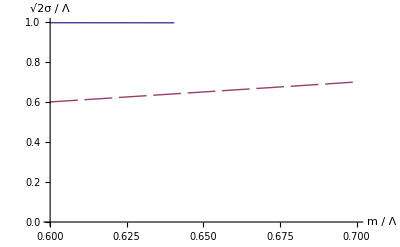

```mathematica
phase = Sqrt[r1[u]]
Plot[{sig[u, ml Λ] / Λ,ml},{ml, 0.60,0.70},  
          PlotStyle->{Thick, {Thick, Dashing[{0.05,0.012}]}}, PlotRange->{0., ⅇ^(-u/2)},
	AxesLabel->{ "m / Λ", "√2σ / Λ"}, PlotPoints->20, MaxRecursion->0]
```

```mathematica
sig[u, 0.69 Λ]
```

-9.90418+7.03226×10^-20 ⅈ

```mathematica
u=0.2;
Sqrt[r1[u]]
FindRoot[ sig[u, μ Λ] == μ Λ,{ μ,Sqrt[r1[u]]} ]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.70231

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

FindRoot::nlnum: The function value {-4.605170185988092` + 0.0003333333333333333` (Log[36.25384938440364`  + Plus[« 2 »] Plus[« 2 »]] + Log[36.25384938440364`  + Plus[« 2 »] Plus[« 2 »]] + Log[36.25384938440364`  + Plus[« 2 »] Plus[« 2 »]] + Log[36.25384938440364`  + Plus[« 2 »] Plus[« 2 »]] + Log[36.25384938440364`  + Plus[« 2 »] Plus[« 2 »]] + Log[36.25384938440364`  + Plus[« 2 »] Plus[« 2 »]] + Log[36.25384938440364`  + Plus[« 2 »] Plus[« 2 »]] + « 38 » + Log[36.25384938440364`  + Plus[« 2 »] Plus[« 2 »]] + Log[36.25384938440364`  + Plus[« 2 »] Plus[« 2 »]] + Log[36.25384938440364`  + Plus[« 2 »] Plus[« 2 »]] + Log[36.25384938440364`  + Plus[« 2 »] Plus[« 2 »]] + Log[36.25384938440364`  + Plus[« 2 »] Plus[« 2 »]] + « 2950 »), -« 18 » + « 1 »} is not a list of numbers with dimensions {2} at {σ, DD} = {18.09674836071919`, 36.25384938440364`}.

ReplaceAll::reps: {FindRoot[sys[0.2`, 10 μ], {σ, Λ Exp[-0.2`/2.`] 2.`}, {DD, Λ^2 (1 - Exp[Times[« 2 »]]) 2.`}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

{μ→0.568792-2.02786×10^-6 ⅈ}

```mathematica
Plot[{μ^2 - Log[μ^2] - 1, -1. - Log[μ^2], 2(1+μ)(1-μ)^2}, {μ, 0., 1.1}, PlotStyle->{Thick,{Thick,Dashed}}, PlotRange->{0.,3}]
```

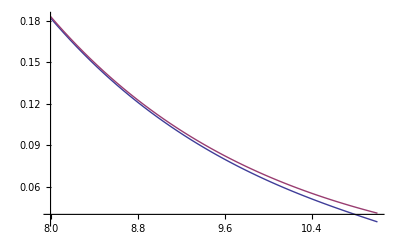

```mathematica
Plot[{sig[u, 0.02], Λ Exp[-u/2.0], Λ Exp[ (- u)/2.0 Λ^2/(Λ^2 - m0^2)]}, {u,8.0, 11.0}]
```

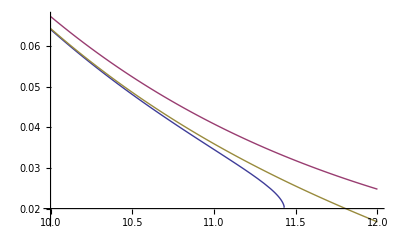

```mathematica
Plot[{sig[u, m], Λ ⅇ^(-u/2), Λ ( ⅇ^(-u/2)  - m^2/Λ^2 Sinh[u/2])}, {u, 10.0, 12.}]
```

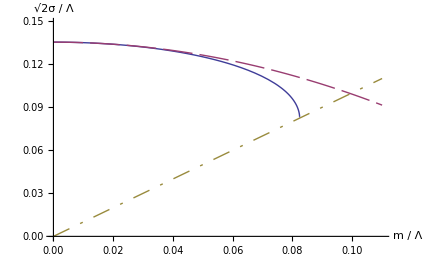

```mathematica
Plot[{sig[u, ml Λ] / Λ,( ⅇ^(-u/2)  - (ml Λ)^2/Λ^2 Sinh[u/2]), ml},{ml, 0.0 / Λ, 1.1 / Λ}, PlotRange->{0.0, 1.1 ⅇ^(-u/2)}, 
          PlotStyle->{Thick, {Thick, Dashing[{0.05,0.012}]}, {Thick, Dashing[{0.03,0.02,0.005, 0.02}]}},
	AxesLabel->{ "m / Λ", "√2σ / Λ"}]
```

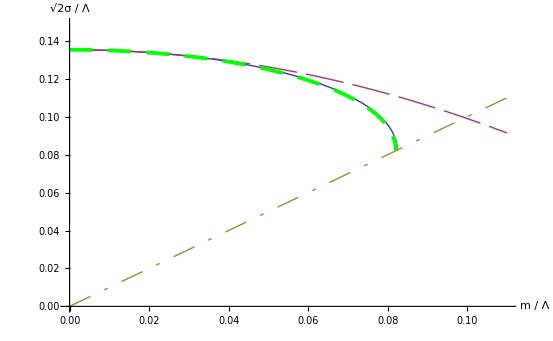

```mathematica
Show[   %, Plot[{asig[ u, ml Λ ] / Λ}, {ml, 0.0, ⅇ^(-(u+1)/2)}, PlotStyle->{{Thickness[0.005],Dashing[{0.03,0.02}],Green}}]   ]
```

```mathematica
m=0.02
```

0.02

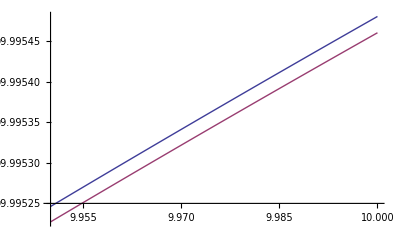

```mathematica
Plot[{dd[u, 0.02], Λ^2 (1 - ⅇ^-u) }, {u , 9.95, 10.0}]
```

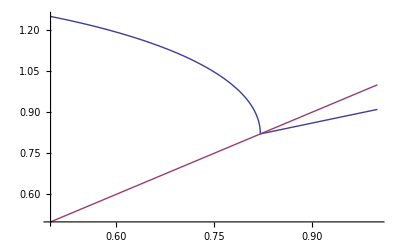

```mathematica
Plot[{asig[u,m],m},{m,0.5,1.0}]
```

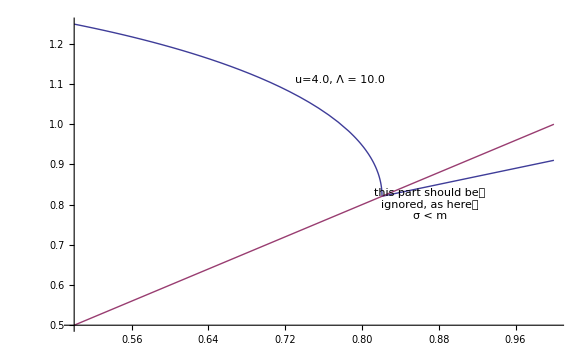

-Graphics-

```mathematica
Subscript[m, min] = 0.0;
Subscript[m, max]= 1.0;
MM = 50;
dm = (Subscript[m, max] - Subscript[m, min])/MM;
mpos =Table[Null,{MM}];
ssig = Table[Null,{MM}];
ddd = Table[Null, {MM}];
addd = Table[Null, {MM}];
EEE = Table[Null,{MM}];
sigcorr = Table[Null, {MM}];
assig = Table[Null, {MM}];
abssq[k_,l_] := (Abs[ ssig[[l+1]] - mpos[[l+1]] circ[[k+1]]])^2
```

```mathematica
For [ l = 0, l < MM, l++, 
mpos[[l+1]] = Subscript[m, min] + dm l;
ssig[[l+1]] = sig[u, mpos[[l+1]] ];
ddd[[l+1]] = dd[u,mpos[[l+1]] ];
addd[[l+1]] = Λ^2 - (ssig[[l+1]])^2 - (mpos[[l+1]])^2;
EEE[[l+1]] = 1/NN∑_(k=0)^(NN-1) (abssq[k,l] Log[ abssq[k,l]/Λ^2] -( ddd[[l+1]] + abssq[k,l]) Log [ (ddd[[l+1]] +abssq[k,l])/Λ^2] ) + ddd[[l+1]] + u (Abs[ssig[[l+1]]])^2;
EEE[[l+1]] = 1/Λ^2 EEE[[l+1]];
sigcorr[[l+1]] = Λ( ⅇ^(-u/2)  - (mpos[[l+1]])^2/Λ^2 Sinh[u/2]);
assig[[l+1]] = asig[u,mpos[[l+1]]];
];
Evsm = Partition[Riffle[mpos,EEE ],2];
mvsm = Partition[Riffle[mpos,mpos],2];
sigvsm = Partition[Riffle[mpos,ssig],2];
sigcorrvsm = Partition[Riffle[mpos,sigcorr],2];
dvsm = Partition[Riffle[mpos,ddd],2];
assigvsm = Partition[Riffle[mpos,assig],2];
adddvsm = Partition[Riffle[mpos, addd], 2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

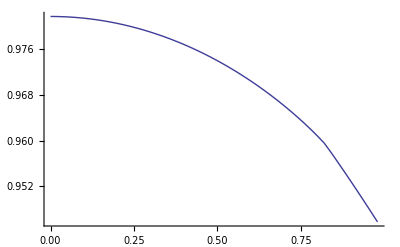

```mathematica
ListPlot[Evsm, Joined->True]
```

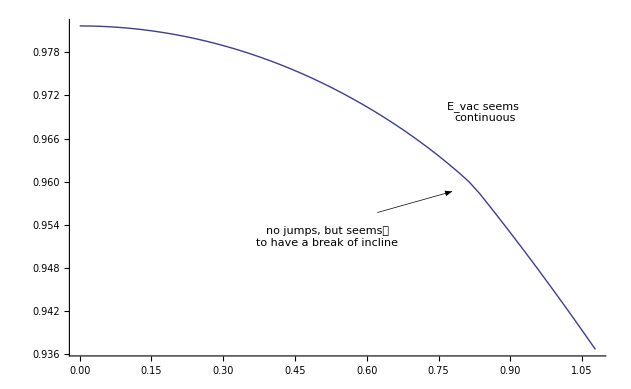

-Graphics-

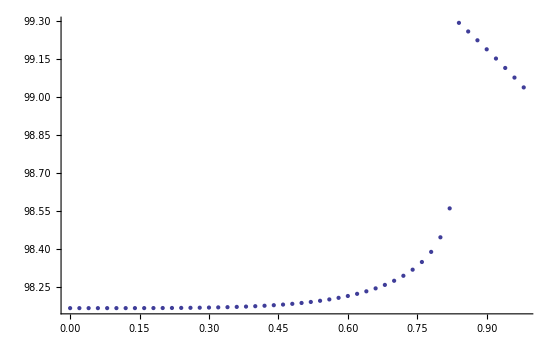

```mathematica
ListPlot[dvsm]
```

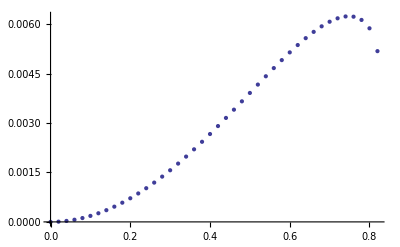

```mathematica
ListPlot[ Table[ {mpos[[n]], ddd[[n]] -addd[[n]]}, {n,1,50} ] ]
```

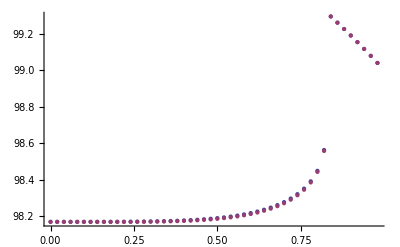

```mathematica
ListPlot[{dvsm,adddvsm}]
```

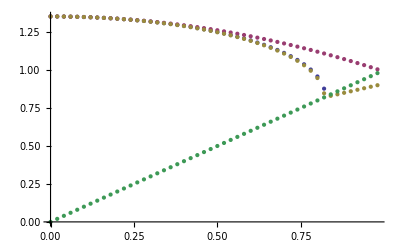

```mathematica
ListPlot[{sigvsm,sigcorrvsm,assigvsm,mvsm}]
```

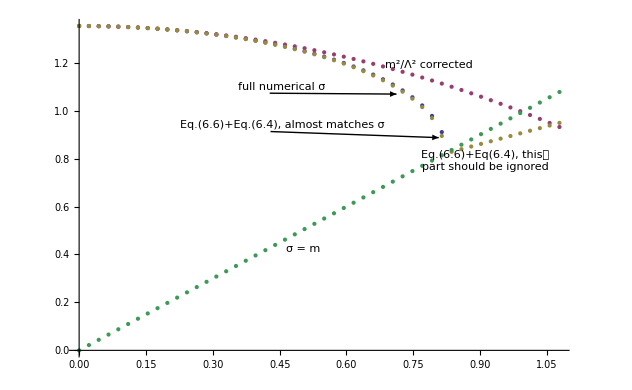

-Graphics-

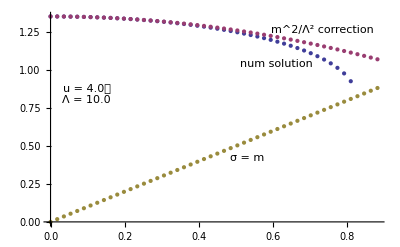

-Graphics-

```mathematica
Λ ⅇ^(-u/2)
```

1.35335